```mathematica
ρint[x_,T_]=(x^(1/2)(x+2/T)^(1/2)(x+1/T)^2)/(Exp[x+1/T]+1);
ρintp[x_,T_]=D[ρint[x,T], T];
pint[x_,T_]=(x^(3/2)(x+2/T)^(3/2))/(Exp[x+1/T]+1);
pintp[x_,T_]=D[pint[x,T], T];
```

```mathematica
gSM=106.75;
gDM=2 2;
```

```mathematica
ρ[T_]:=π^2/30 gSM T^4+T^4/(2 π^2)NIntegrate[ρint[x,T],{x,0,1000}]gDM
ρp[T_]:=π^2/30 gSM 4 T^3+ 4 T^3/(2 π^2)NIntegrate[ρint[x,T],{x,0,1000}]gDM+T^4/(2 π^2)NIntegrate[ρintp[x,T],{x,0,1000}]gDM
p[T_]:=1/3 π^2/30 gSM T^4+T^4/(6 π^2)NIntegrate[pint[x,T],{x,0,1000}]gDM
pp[T_]:=1/3 π^2/30 gSM 4 T^3+4 T^3/(6 π^2)NIntegrate[pint[x,T],{x,0,1000}]gDM+T^4/(6 π^2)NIntegrate[pintp[x,T],{x,0,1000}]gDM
s[T_]:=(ρ[T]+p[T])/T
w[T_]:=p[T]/ρ[T]
cs2[T_]:=pp[T]/ρp[T]
gr[T_]:=ρ[T]/(π^2/30 T^4)
gs[T_]:=s[T]/((2 π^2)/45 T^3)
```

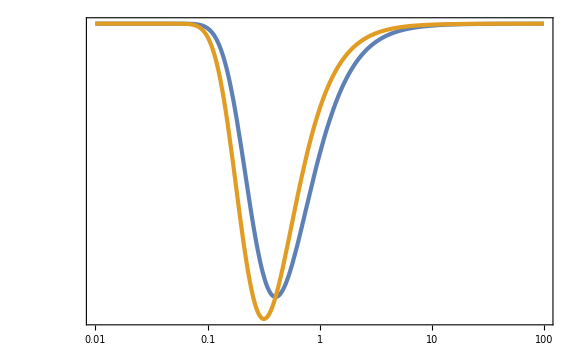

```mathematica
LogLogPlot[{w[T],cs2[T]},{T,0.01,100}]
```

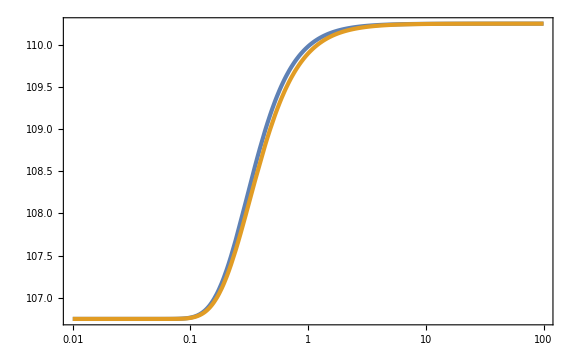

```mathematica
LogLinearPlot[{gr[T],gs[T]},{T,0.01,100}]
```

```mathematica
Tin=10000;
ain=1;
sin=s[Tin]
a[T_]:=ain sin^(1/3)/s[T]^(1/3)
```

4.83611×10^13

```mathematica
aTList=Table[{a[10^lnT],10^lnT},{lnT,-4,4,0.01}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

General::munfl: 7.37138×10^-14 2.38772×10^-296 is too small to represent as a normalized machine number; precision may be lost.

```mathematica
Tint[a_]=Interpolation[aTList][a];
```

```mathematica
Tout=10^-4;
aout=a[Tout]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

1.01081×10^8

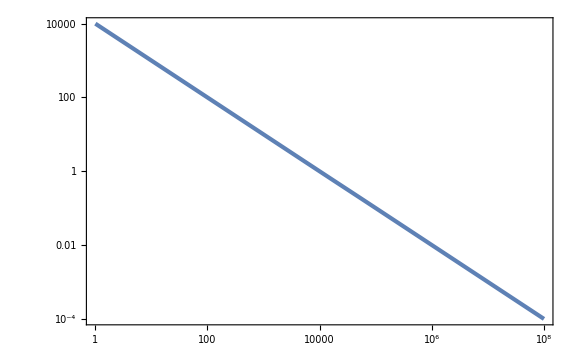

```mathematica
LogLogPlot[Tint[a],{a,ain,aout}]
```